```mathematica
ClearAll["Global`*"]
```

## Step response

### TF function

```mathematica
TFstep=Simplify[OutputResponse[1/(s+1)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Horizontal Dashed Line

```mathematica
stepLineAbove=Line[{{0,TFstableValue},{4,TFstableValue}}];
```

### Tangent Line

```mathematica
a=0.01;
tangentLine =(D[TFstep,t]/.t->a)×(t-a) + (TFstep/.t->a);
```

### Vertical Dashed Line

```mathematica
s=Solve[tangentLine==TFstableValue];
x=s[[All,1,2]][[1]];
vertLine=Line[{{x,0},{x,TFstableValue*1.2}}];
```

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Style[text, 18,FontSlant->Plain,FontFamily->"Times New Roman"];
```

#### Horizontal size

```mathematica
horSizeLeft={0,TFstableValue+0.1};
horSizeRight={x,TFstableValue+0.1};
horSize={arrowsHeads,Arrow[{horSizeLeft,horSizeRight}]};
horSizeText=Text[
sizeText[T],
{
Abs[(horSizeLeft[[1]]-horSizeRight[[1]])/2],
horSizeLeft[[2]]+0.05
}
];
```

#### Vertical size

```mathematica
verSizeStart={3,0};
verSizeEnd={3,TFstableValue};
verSize={arrowsHeads,Arrow[{verSizeStart,verSizeEnd}]};
verSizeText=Text[
sizeText[k],
{
verSizeStart[[1]]+0.12,
Abs[(verSizeStart[[2]]-verSizeEnd[[2]])/2]
}
];
```

### Plot

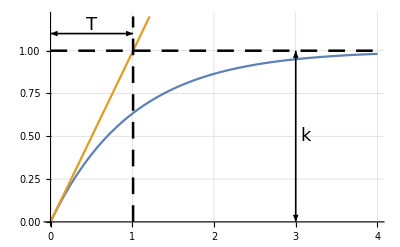

```mathematica
stepRespPic=Plot[{TFstep,tangentLine}, {t, 0, 4},
AxesStyle->Directive[Black, FontSize->9],
GridLines->Automatic,
PlotStyle->Automatic,
PlotRange->{{0,4},{0,TFstableValue*1.2}},
Epilog->{
{Directive[Dashing[{0.03,0.02}],Black,Thickness[0.0045]],stepLineAbove},
{Directive[Dashing[{0.03,0.02}],Black,Thickness[0.0045]],vertLine},
{Directive[Thickness[0.003]],horSize},
{horSizeText},
{Directive[Thickness[0.003]],verSize},
{verSizeText}
}
]
```

```mathematica
Export["step.png",stepRespPic,ImageResolution->900];
```